# Exponential growth

```mathematica
ClearAll["Global`*"]
```

## Initiation

Growth constant :

```mathematica
k:=0.1
```

Initial population :

```mathematica
Subscript[P, 0]=100
```

100

## Differential equation with initial conditions

```mathematica
equ=P'[t]==k P[t];
```

```mathematica
cond=P[0]==Subscript[P, 0];
```

## DSolve

```mathematica
DS=DSolve[{equ,cond},P[t],t]//FullSimplify
```

{{P[t]→100. ⅇ^(0.1 t)}}

```mathematica
P[t_]=DS[[1,1,2]]
```

100. ⅇ^(0.1 t)

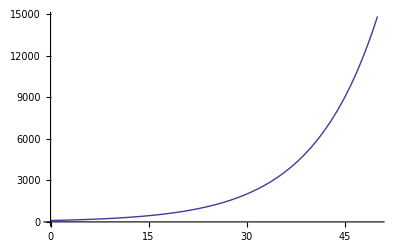

```mathematica
Plot[P[t],{t,0,50}]
```